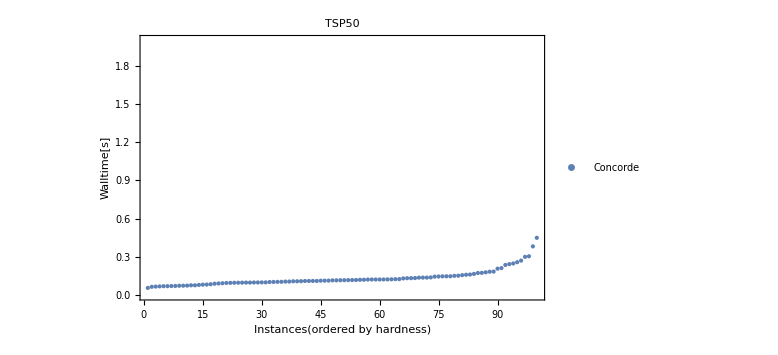

```mathematica
concorde=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/concorde/50n_0423-1647.csv", Numeric->True];
concorde=Delete[concorde,1];
(*{stime|walltime|proctime}*)
concorde=Part[#,2]&/@concorde;
concorde=Sort[concorde];
plot=Show[
ListPlot[{concorde},
Frame->True, FrameLabel->{"Instances(ordered by hardness)","Walltime[s]"},
PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"Concorde"}],{0.1,0.85}]],
PlotRange->{Automatic,{Max[Floor[Min[concorde]],0],Ceiling[Max[concorde]]+1}},
PlotLabel->Style["TSP50"],
AxesOrigin->{0,0},
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/Plots/Concorde/tsp50.png",plot];
```

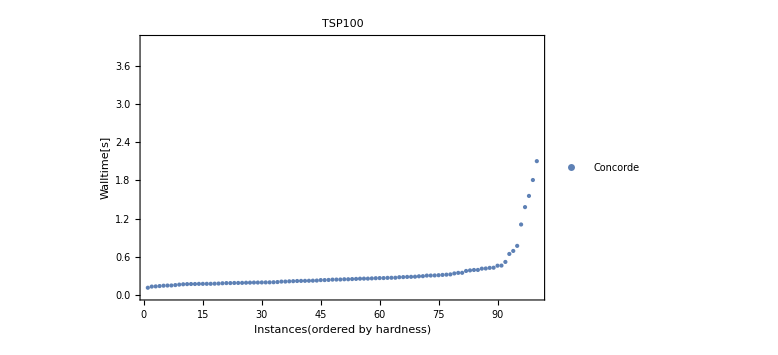

```mathematica
concorde=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/concorde/100n_0423-1653.csv", Numeric->True];
concorde=Delete[concorde,1];
(*{stime|walltime|proctime}*)
concorde=Part[#,2]&/@concorde;
concorde=Sort[concorde];
plot=Show[
ListPlot[{concorde},
Frame->True, FrameLabel->{"Instances(ordered by hardness)","Walltime[s]"},
PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"Concorde"}],{0.1,0.85}]],
PlotRange->{Automatic,{Max[Floor[Min[concorde]],0],Ceiling[Max[concorde]]+1}},
PlotLabel->Style["TSP100"],
AxesOrigin->{0,0},
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/Travel-the-Same-Path/results/Plots/Concorde/tsp100.png",plot];
```